# Plotting with DaMaSCUS v1.0

This Mathematica notebook creates plots of the basic results of a successful DaMaSCUS run.

## Initialization Cells

```mathematica
SetDirectory[NotebookDirectory[]];
<<DaMaSCUStoolbox.m;
Needs["ErrorBarPlots`"];
```

The DaMaSCUStoolbox Mathematica package is part of DaMaSCUS (available at https://github.com/temken/DaMaSCUS). It is a collection of useful functions and serves as a little tool box for plotting DaMaSCUS results. For a list of functions type ?DaMaSCUS_Toolbox`*

```mathematica
?DaMaSCUStoolbox`*
```

## Simulation Parameter

Enter the simulation IDs, whose results will be plotted and compared. The plots will be saved in a folder named after the first ID.

```mathematica
SimID={"MS10","MS50"};
DetectionType={"CRESST-II","CRESST-II"};
CreateDirectory[SimID[[1]]];
date={15,02,2016};
time={0,0,0};
v♁=EarthVelocity[FractionalDays[date,time]];
IsodetectionRings=36;
```

## Plots

### Dark Matter Density

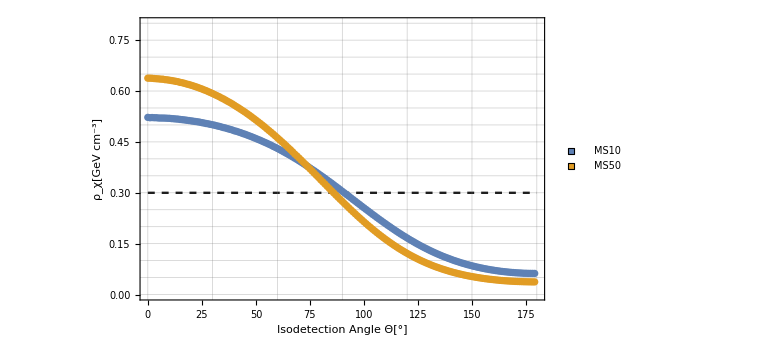

```mathematica
PR={All,{0.0,0.8}};
ρPlotList={Plot[0.3,{x,0,180},PlotStyle->{Dashed,Black},PlotRange->PR]};
For[i=1,i≤Length[SimID],i++,
ρlist=Import[StringJoin["../results/",SimID[[i]],".rho"],"Data"];
ρplotMC=ErrorListPlot[ρlist,PlotRange->PR,PlotStyle->ColorData[97,"ColorList"][[i]]];
AppendTo[ρPlotList,ρplotMC];
]
ρPlot=Legended[
Show[ρPlotList,
AspectRatio->1/GoldenRatio,
PlotRange->PR,
Frame->True,
FrameLabel->{{"ρ_χ[GeV cm^-3]",None},{"Isodetection Angle Θ[°]",None}},
GridLines->{Range[0,180,30],Range[PR[[2,1]],PR[[2,2]],0.05]},
FrameTicks->Automatic,
ImageSize->Large
]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/DMdensity.pdf",%];
```

### Normalized Speed Distribution

DaMaSCUS saves a histogram for each of the 180 isodetection rings, which can be plotted here. Note that here the histograms are normalized and estimate the density distribution function.

MC results:

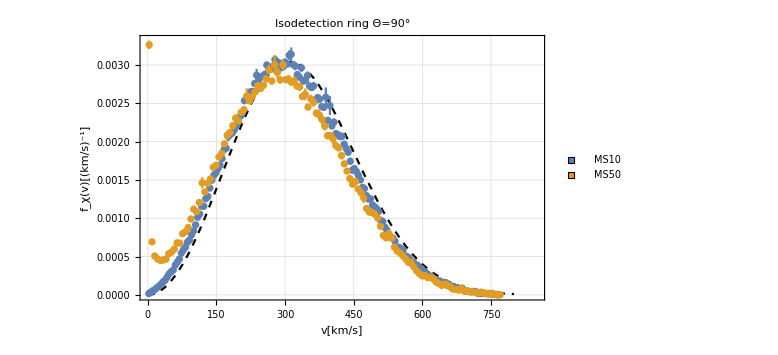

```mathematica
PR={{0,850},All};
IsoRing=90;
(*Analytic result for transparent Earth*)
fPlotList={Plot[km/sec SpeedDistribution[v km/sec,v♁],{v,0,800},PlotRange->PR,PlotStyle->{Black,Dashed,Thick},PlotPoints->2,ImageSize->Large]};
For[i=1,i≤Length[SimID],i++,
HistogramMC = Import[StringJoin["../results/",SimID[[i]],"_histograms/Speed.",ToString[IsoRing]],"Data"];
HistogramMCerror = Table[{{InUnits[HistogramMC[[i,1]],km/sec],InUnits[HistogramMC[[i,2]],sec/km]},ErrorBar[InUnits[HistogramMC[[i,3]],km/sec],InUnits[HistogramMC[[i,4]],sec/km]]},{i,1,Length[HistogramMC]}];
SpeedPlotMC = ErrorListPlot[HistogramMCerror,PlotRange->PR,PlotStyle->ColorData[97,"ColorList"][[i]]];
AppendTo[fPlotList,SpeedPlotMC];
]
Legended[
Show[fPlotList,
PlotRange->PR,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameLabel->{{"f_χ(v)[(km/s)^-1]",None},{"v[km/s]",None}},GridLines->Automatic,
FrameTicks->Automatic,
PlotLabel->"Isodetection ring Θ="<>ToString[180IsoRing  / IsodetectionRings]<>"°"
]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/SpeedDistr_"<>ToString[180IsoRing  / IsodetectionRings]<>".pdf",%];
```

### Average Speed

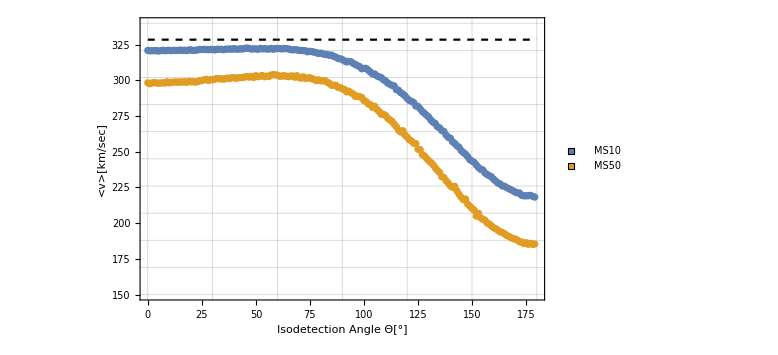

{328.459,268.713}

```mathematica
PR={All,{150,340}};
c=InUnits[AverageDMSpeed[v♁],km/sec];
vPlotList={Plot[c,{x,0,180},PlotStyle->{Black,Dashed},PlotRange->PR]};
For[i=1,i≤Length[SimID],i++,
vlist=Import[StringJoin["../results/",SimID[[i]],".speed"],"Data"];
vlist=Table[{vlist[[i,1]],InUnits[vlist[[i,2]],km/sec],InUnits[vlist[[i,3]],km/sec]},{i,1,Length[vlist]}];
AppendTo[vPlotList,ErrorListPlot[vlist,PlotRange->PR,PlotStyle->ColorData[97,"ColorList"][[i]]]];
]
Legended[
Show[vPlotList,
PlotRange->PR,
Frame->True,
FrameLabel->{{"<v>[km/sec]",None},{"Isodetection Angle Θ[°]",None}},
GridLines->{Range[0,180,30],Range[PR[[2,1]],PR[[2,2]],(PR[[2,2]]-PR[[2,1]])/10]},
FrameTicks->Automatic,
ImageSize->Large
]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/AverageSpeed.pdf",%];
{c,Mean[vlist][[2]]}
```

### η-Function

Based on the histogram estimates of the speed distribution we can compare the η-functions of the MC to the analytic result for the SHM.

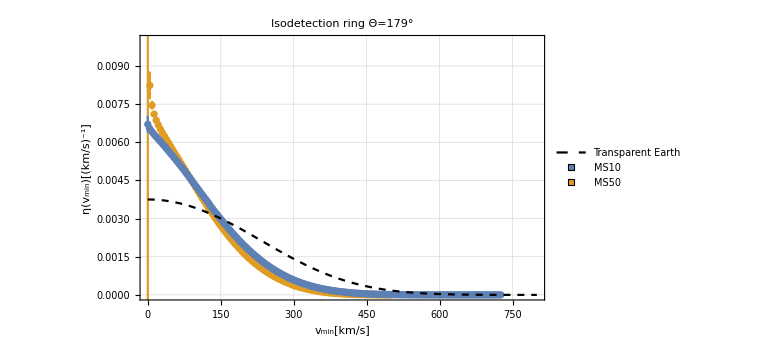

```mathematica
IsoRing=179;
PR={{0,800},{0,0.01}};
PlotList={Plot[km/sec EtaFunction[x km/sec ,v♁],{x,0,800},PlotStyle->{Black,Dashed},PlotLegends->{"Transparent Earth"}]};
For[i=1,i≤Length[SimID],i++,
listη=Import[StringJoin["../results/",SimID[[i]],"_histograms/","eta.",ToString[IsoRing]],"Data"];
listη=Table[{{sec/km listη[[i,1]],km/sec listη[[i,2]]},ErrorBar[sec/km listη[[i,3]],km/sec listη[[i,4]]]},{i,1,Length[listη]}];
PrependTo[PlotList,ErrorListPlot[listη,PlotStyle->ColorData[97,"ColorList"][[i]]]];
]
Legended[
Show[PlotList,
PlotRange->PR,
Frame->True,
FrameLabel->{{"η(v_min)[(km/s)^-1]",None},{"v_min[km/s]",None}},
GridLines->Automatic,
ImageSize->Large,
PlotLabel->"Isodetection ring Θ="<>ToString[180IsoRing  / IsodetectionRings]<>"°"
]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/EtaFunction_"<>ToString[180IsoRing  / IsodetectionRings]<>".pdf",%];
```

### dR/dE_R-Recoil spectrum

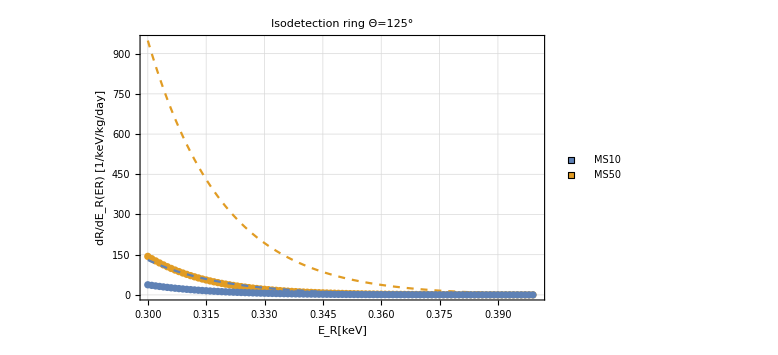

```mathematica
IsoRing=125;
PlotList={};
For[i=1,i≤Length[SimID],i++,
dRlist=Import[StringJoin["../results/",SimID[[i]],"_histograms/dRdE.",ToString[IsoRing]],"Data"];
For[j=1,j≤Length[dRlist],j++,
dRlist[[j,1]]=InUnits[dRlist[[j,1]],keV];
dRlist[[j,2]]=InUnits[dRlist[[j,2]],1/(keV kg day)];
dRlist[[j,3]]=InUnits[dRlist[[j,3]],keV];
dRlist[[j,4]]=InUnits[dRlist[[j,4]],1/(keV kg day)];
dRlist[[j,5]]=InUnits[dRlist[[j,5]],1/(keV kg day)];
];
PrependTo[PlotList,ListPlot[dRlist[[All,{1,5}]],Joined->True,PlotStyle->{Dashed,ColorData[97,"ColorList"][[i]]},PlotRange->All]];
dRlistError=Table[{{dRlist[[i,1]],dRlist[[i,2]]},ErrorBar[dRlist[[i,3]],dRlist[[i,4]]]},{i,1,Length[dRlist]}];
PrependTo[PlotList,ErrorListPlot[dRlistError,PlotStyle->ColorData[97,"ColorList"][[i]]]];
]
Legended[
Show[PlotList,
PlotRange->{{0.3,0.4},All},
Frame->True,
FrameLabel->{{"dR/dE_R(ER) [1/keV/kg/day]",None},{"E_R[keV]",None}},
GridLines->Automatic,
ImageSize->Large,
PlotLabel->"Isodetection ring Θ="<>ToString[180IsoRing  / IsodetectionRings]<>"°"
]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/dRdE_"<>DetectionType[[1]]<>"_"<>ToString[180IsoRing  / IsodetectionRings]<>".pdf",%];
```

Log-log plot

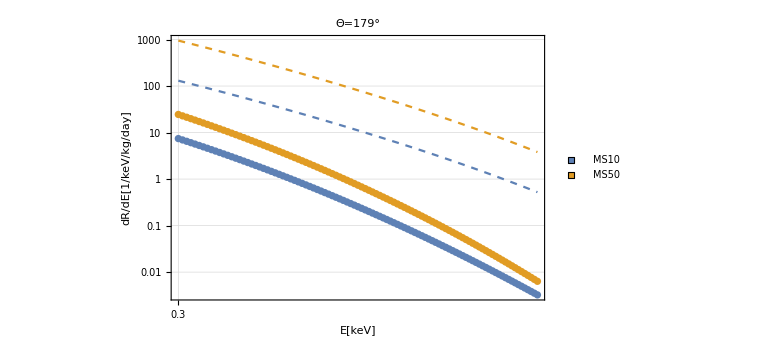

```mathematica
IsoRing=179;
list={};
For[i=1,i≤Length[SimID],i++,
l=Import[StringJoin["../results/",SimID[[i]],"_histograms/dRdE.",ToString[IsoRing]],"Data"];
For[j=1,j≤Length[l],j++,
l[[j,1]]=InUnits[l[[j,1]],keV];
l[[j,2]]=InUnits[l[[j,2]],1/(keV kg day)];
l[[j,3]]=InUnits[l[[j,3]],keV];
l[[j,4]]=InUnits[l[[j,4]],1/(keV kg day)];
l[[j,5]]=InUnits[l[[j,5]],1/(keV kg day)];
];
AppendTo[list,ListLogLogPlot[l[[All,{1,2}]],PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[i]]]];
AppendTo[list,ListLogLogPlot[l[[All,{1,5}]],PlotRange->All,Joined->True,PlotStyle->{ColorData[97,"ColorList"][[i]],Dashed,Thick}]];
]
Legended[
Show[list,PlotRange->All,Frame->True,GridLines->Automatic,FrameLabel->{{"dR/dE[1/keV/kg/day]",None},{"E[keV]",None}},PlotLabel->"Θ="<>ToString[180IsoRing  / IsodetectionRings]<>"°",ImageSize->Large]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/dRdE_"<>DetectionType[[1]]<>"_"<>ToString[180IsoRing  / IsodetectionRings]<>"_log.pdf",%];
```

### Total Event Rate

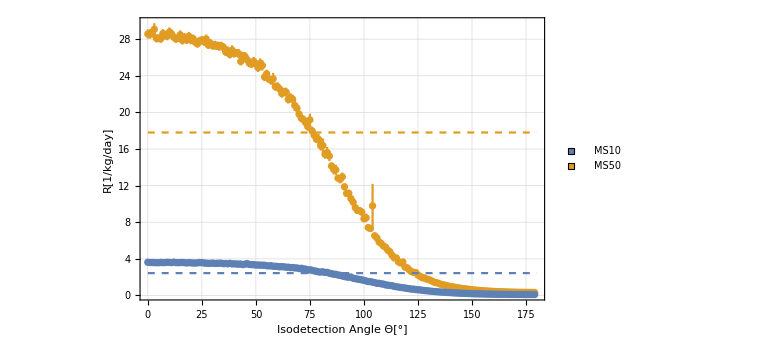

```mathematica
PR={All,All};
RPlotList={};
For[i=1,i≤Length[SimID],i++,
Rlist=Import[StringJoin["../results/",SimID[[i]],".CRESST-II"],"Data"];
AppendTo[RPlotList,Plot[InUnits[Rlist[[1,4]],1/(kg day)],{x,0,180},PlotStyle->{Dashed,Thick,ColorData[97,"ColorList"][[i]]}]];
RlistUnits=Table[{Rlist[[i,1]],InUnits[Rlist[[i,2]],1/(kg day)],InUnits[Rlist[[i,3]],1/(kg day)]},{i,1,Length[Rlist]}];
PrependTo[RPlotList,ErrorListPlot[RlistUnits,PlotRange->PR,PlotStyle->ColorData[97,"ColorList"][[i]]]];
]
RPlot=
Legended[
Show[RPlotList,
PlotRange->PR,
Frame->True,
FrameLabel->{{"R[1/kg/day]",None},{"Isodetection Angle Θ[°]",None}},
GridLines->Automatic,
FrameTicks->Automatic,
ImageSize->Large]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/R_"<>DetectionType[[1]]<>".pdf",%];
```

Log-log plot

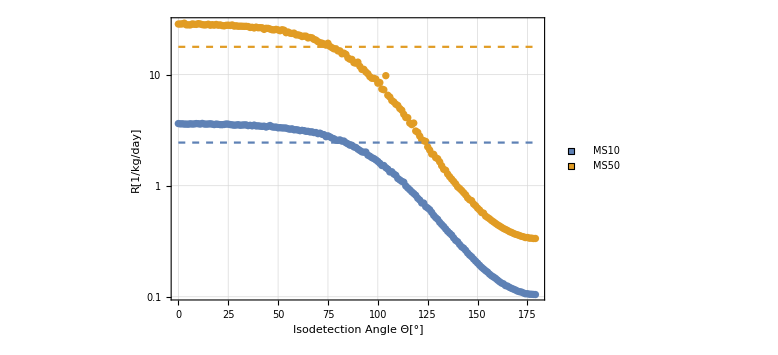

```mathematica
PR={All,{0.0,All}};
RPlotList={};
For[i=1,i≤Length[SimID],i++,
Rlist=Import[StringJoin["../results/",SimID[[i]],".CRESST-II"],"Data"];
AppendTo[RPlotList,LogPlot[InUnits[Rlist[[1,4]],1/(kg day)],{x,0,180},PlotStyle->{Dashed,Thick,ColorData[97,"ColorList"][[i]]}]];
RlistUnits=Table[{Rlist[[i,1]],InUnits[Rlist[[i,2]],1/(kg day)]},{i,1,Length[Rlist]}];
PrependTo[RPlotList,ListLogPlot[RlistUnits,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[i]]]];
]
RPlot=
Legended[
Show[RPlotList,
PlotRange->All,
Frame->True,
FrameLabel->{{"R[1/kg/day]",None},{"Isodetection Angle Θ[°]",None}},
ImageSize->Large,
Axes->False,
GridLines->Automatic]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/R_"<>DetectionType[[1]]<>"_log.pdf",%];
```

### Total Event Rate - normalized to transparent Earth results)

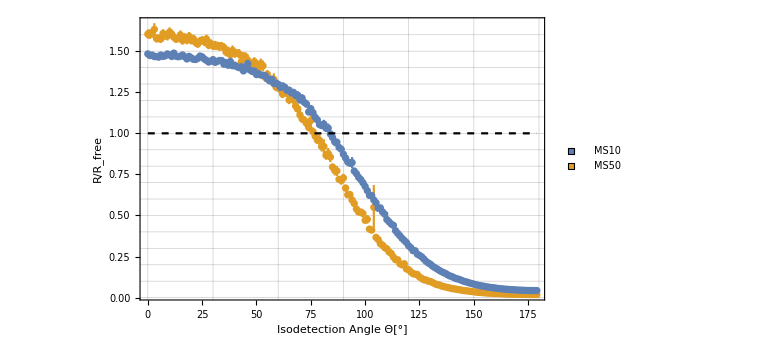

0.761237

```mathematica
PR={All,{0.0,All}};
RPlotList={Plot[1,{x,0,179},PlotStyle->{Dashed ,Black},PlotRange->PR]};
For[i=1,i≤Length[SimID],i++,
Rlist=Import[StringJoin["../results/",SimID[[i]],".",DetectionType[[i]]],"Data"];
NormalizedRlist=Table[{Rlist[[i,1]],Rlist[[i,2]]/Rlist[[1,4]],Rlist[[i,3]]/Rlist[[1,4]]},{i,1,Length[Rlist]}];
PrependTo[RPlotList,ErrorListPlot[NormalizedRlist,PlotRange->PR,PlotStyle->ColorData[97,"ColorList"][[i]]]];
]
RPlot=
Legended[
Show[RPlotList,
PlotRange->PR,
Frame->True,
FrameLabel->{{"R/R_free",None},{"Isodetection Angle Θ[°]",None}},
GridLines->{Range[0,180,30],Range[0.0,2.0,0.1]},
FrameTicks->Automatic,
ImageSize->Large]
,
PointLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID,LegendMarkers->Graphics[Rectangle[]]]
]
Export[SimID[[1]]<>"/R_normalized_"<>DetectionType[[1]]<>".pdf",%];
Mean[NormalizedRlist][[2]]
```

### Diurnal modulation at experimental site

Experiment’s coordinates (latitude, longitude) in °

```mathematica
GranSasso={45.454°,13.576°};
SUPL={-37.07°,142.81°};
CJPL={28.1532°,101.7114°};
INO={9.967°,77.267°};
SierraGrande={-41.67°,-66.38°};
Canfranc={42.7492°,-0.5164°};
```

Choose one:

```mathematica
exp=SUPL;
```

This will show its motion through the isodetection rings on the day specified in the beginning.

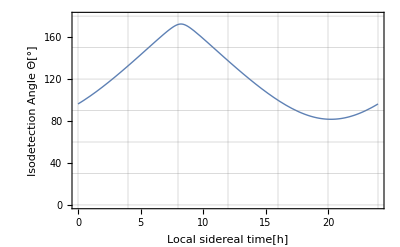

```mathematica
Plot[DetectorAngle[x 3600,date,exp],{x,0,24},
PlotRange->{{0,24},{0,180}},
AspectRatio->1/GoldenRatio,
PlotStyle->Thick,
Frame->True,
FrameLabel->{{"Isodetection Angle Θ[°]",None},{"Local sidereal time[h]",None}},
GridLines->{Range[0,24,4],Range[0,180,30]}
]
```

Plot the diurnal signal modulation

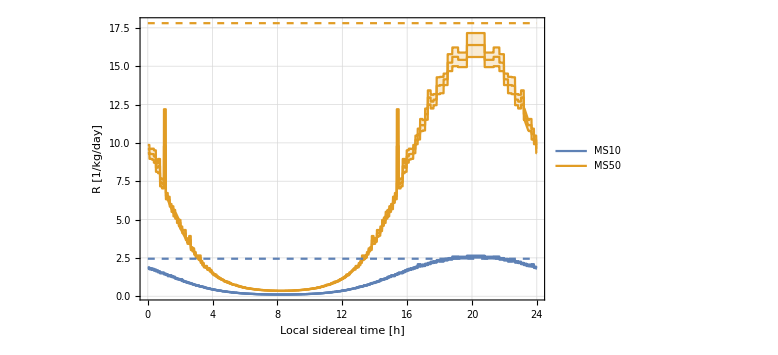

```mathematica
PR={{0,24},All};
PlotList={};
For[i=1,i≤Length[SimID],i++,
Rlist=Import[StringJoin["../results/",SimID[[i]],".",DetectionType[[i]]],"Data"];
PrependTo[PlotList,Plot[InUnits[Rlist[[1,4]],1/(kg day)],{x,0,24},PlotRange->PR,PlotStyle->{ColorData[97,"ColorList"][[i]],Dashed}]];
EventRateMC = Rlist[[All,{1,2,3}]];
LocalEventRate[last_,{lat_?NumericQ,lon_?NumericQ}]:=Module[{isoring},
isoring=Ceiling[DetectorAngle[last,date,{lat,lon}] IsodetectionRings / 180 ];
Return[InUnits[EventRateMC[[isoring,{2,3}]],1/(kg day)]]
];
PrependTo[PlotList,Plot[{LocalEventRate[x 3600,exp][[1]],LocalEventRate[x 3600,exp][[1]]+LocalEventRate[x 3600,exp][[2]],LocalEventRate[x 3600,exp][[1]]-LocalEventRate[x 3600,exp][[2]]},{x,0,24},
PlotStyle->{{ColorData[97,"ColorList"][[i]]},{ColorData[97,"ColorList"][[i]]},{ColorData[97,"ColorList"][[i]]}},
PlotRange->PR,
PlotStyle->Thick,
Filling->{3->{2}}
]
];
]
Legended[
Show[PlotList,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameLabel->{{"R [1/kg/day]",None},{"Local sidereal time [h]",None}},
GridLines->Automatic,
FrameTicks->Automatic,
ImageSize->Large
]
,
LineLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID]
]
Export[SimID[[1]]<>"/DiurnalModulation_"<>DetectionType[[1]]<>".pdf",%];
```

Logarithmic plot:

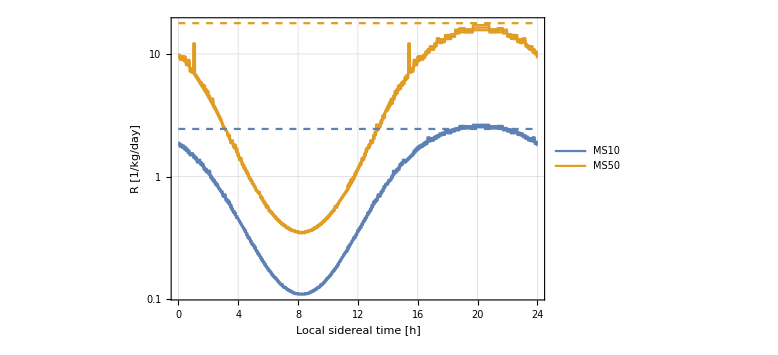

```mathematica
PR={{0,24},All};
PlotList={};
For[i=1,i≤Length[SimID],i++,
Rlist=Import[StringJoin["../results/",SimID[[i]],".",DetectionType[[i]]],"Data"];
PrependTo[PlotList,LogPlot[InUnits[Rlist[[1,4]],1/(kg day)],{x,0,24},PlotRange->PR,PlotStyle->{ColorData[97,"ColorList"][[i]],Dashed}]];
EventRateMC = Rlist[[All,{1,2,3}]];
LocalEventRate[last_,{lat_?NumericQ,lon_?NumericQ}]:=Module[{isoring},
isoring=Ceiling[DetectorAngle[last,date,{lat,lon}] IsodetectionRings / 180 ];
Return[InUnits[EventRateMC[[isoring,{2,3}]],1/(kg day)]]
];
PrependTo[PlotList,LogPlot[{LocalEventRate[x 3600,exp][[1]],LocalEventRate[x 3600,exp][[1]]+LocalEventRate[x 3600,exp][[2]],LocalEventRate[x 3600,exp][[1]]-LocalEventRate[x 3600,exp][[2]]},{x,0,24},
PlotStyle->{{ColorData[97,"ColorList"][[i]]},{ColorData[97,"ColorList"][[i]]},{ColorData[97,"ColorList"][[i]]}},
PlotRange->PR,
PlotStyle->Thick,
Filling->{3->{2}}
]
];
]
Legended[
Show[PlotList,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameLabel->{{"R [1/kg/day]",None},{"Local sidereal time [h]",None}},
GridLines->Automatic,
(*FrameTicks->Automatic,*)
ImageSize->Large
]
,
LineLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID]
]
Export[SimID[[1]]<>"/DiurnalModulation_"<>DetectionType[[1]]<>"_log.pdf",%];
```

Normalized to the R_free of the transparent Earth:

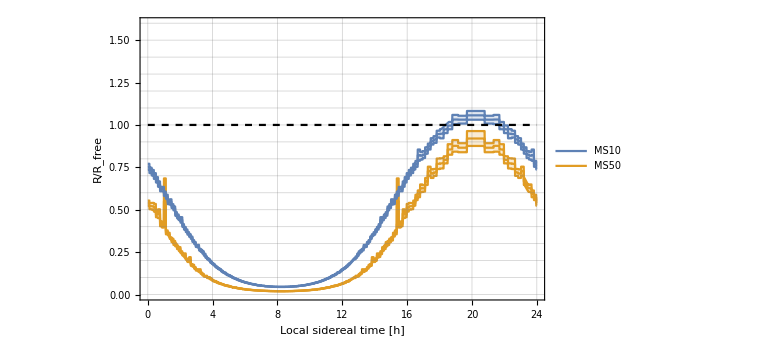

```mathematica
PR={{0,24},{0,1.6}};
PlotList={Plot[1,{x,0,24},PlotRange->PR,PlotStyle->{Black,Dashed}]};
For[i=1,i≤Length[SimID],i++,
Rlist=Import[StringJoin["../results/",SimID[[i]],".",DetectionType[[i]]],"Data"];
EventRateMC = Rlist[[All,{1,2,3}]];
EventRateAnalytic=Rlist[[1,4]];
LocalEventRate[last_,{lat_?NumericQ,lon_?NumericQ}]:=Module[{isoring},
isoring=Ceiling[DetectorAngle[last,date,{lat,lon}] IsodetectionRings / 180 ];
Return[1/EventRateAnalytic EventRateMC[[isoring,{2,3}]]]
];
PrependTo[PlotList,Plot[{LocalEventRate[x 3600,exp][[1]],LocalEventRate[x 3600,exp][[1]]+LocalEventRate[x 3600,exp][[2]],LocalEventRate[x 3600,exp][[1]]-LocalEventRate[x 3600,exp][[2]]},{x,0,24},
PlotStyle->{{ColorData[97,"ColorList"][[i]]},{ColorData[97,"ColorList"][[i]]},{ColorData[97,"ColorList"][[i]]}},
PlotRange->PR,
PlotStyle->Thick,
Filling->{3->{2}}
]
];
]
Legended[
Show[PlotList,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameLabel->{{"R/R_free",None},{"Local sidereal time [h]",None}},
GridLines->{Range[0,24,4],Range[0,2.0,0.1]},
FrameTicks->Automatic,
ImageSize->Large
]
,
LineLegend[Table[ColorData[97,"ColorList"][[i]],{i,1,Length[SimID]}],SimID]
]
Export[SimID[[1]]<>"/DiurnalModulation_normalized_"<>DetectionType[[1]]<>".pdf",%];
```

### Total Event Rate on World Map

Import event rate of one SimID

```mathematica
Rlist=Import[StringJoin["../results/",SimID[[1]],".",DetectionType[[1]]],"Data"];
EventRateMC = Rlist[[All,{1,2,3}]];
EventRateAnalytic=Rlist[[1,4]];
```

An experiments current location in terms of isodetection rings as a function of the fractional days since J2000.0.

```mathematica
IsodetectionRing[n_,{lat_,lon_}]:=Module[{x♁},
x♁=DetectorPosition[n,{lat,lon},0];
Return[InUnits[ArcCos[(x♁.v♁)/(Norm[x♁]Norm[v♁])],°]]
]
```

Normalized total event rate as a function of location on Earth and time.

```mathematica
EventRateMC2=EventRateMC[[All,2]];
GlobalEventRate[{lat_,lon_},date_,time_]:=Module[{isoring},
isoring = Ceiling[IsodetectionRing[FractionalDays[date,time],{lat,lon}] IsodetectionRings / 180 ];
Return[EventRateMC2[[isoring]]/EventRateAnalytic]
]
```

Plot contour plot on world map for certain times during the day.

```mathematica
PlotList={};
Do[
cp2=ContourPlot[GlobalEventRate[{x °,y °},date,{hour,0}],{y,-180,180},{x,-90,90},PlotPoints->60,Contours->40,PlotRange->{{-180,180},{-90,90},All},ClippingStyle->Automatic,
ContourStyle->None,ColorFunction->(Opacity[0.5,ColorData["ThermometerColors"][#]]&),Method->{"TransparentPolygonMesh"->True},PlotLegends->True,ColorFunctionScaling->True];
e1=Legended[GeoGraphics[MapAt[GeoPosition[#[[;;,{2,1}]]]&,cp2[[1,1]],{1}],GeoBackground->GeoStyling["Coastlines"],GeoRange->"World",GeoProjection->"Mollweide",GeoGridLines->Quantity[15,"AngularDegrees"],ImageSize->800,Method->{"TransparentPolygonMesh"->True}],cp2[[2,1]]];
AppendTo[PlotList,e1];
Print[e1];
Export[SimID[[1]]<>"/"<>SimID[[1]]<>"_EarthMap_"<>ToString[hour]<>".jpg",e1];
,
{hour,{0,12}}
]
```

-Graphics-

-Graphics-